## ChooseTmat_all.nb (run ChooseTmat first)

## All maps

#### TRIV maps

```mathematica
TmatallTRIV={TmatBrownAn00,TmatBrownAn25,TmatBrownAn37,TmatBrownAn48,TmatBrownAn60,TmatBrownAn67,TmatBrownAn78,TmatBrownAn96,TmatBrownAn00Pert,TmatIgel,TmatAminzadehBukov0p1,TmatAminzadehGrimsel0p1,TmatBColivine,TmatBCenstatite,TmatMar17,TmatMar17mod,TmatIgel,TmatSSA2023,TmatVosges,TmatVestrum,TmatFrancois,TmatLokajicekWG100lp,TmatLokajicekWG100hp,TmatLokajicekWG600lp,TmatLokajicekWG600hp,TT21TRIV,TmatBecker,TmatIsmailMainpriceTotal,TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatIsmailMainpriceKimberlite,TmatJi1994CastleRock,TmatJi1994AlligatorLake,TmatJi1994NunuvakIsland};
```

#### Brown, Angel, Ross (2016) feldspars

```mathematica
TmatallBrown={TmatBrownAn00,TmatBrownAn25,TmatBrownAn37,TmatBrownAn48,TmatBrownAn60,TmatBrownAn67,TmatBrownAn78,TmatBrownAn96};
```

#### Brown and Abramson (2016) amphiboles

```mathematica
TmatallBrownAbramson={TmatBrownAbramson2016s1,TmatBrownAbramson2016s2,TmatBrownAbramson2016s3,TmatBrownAbramson2016s4,TmatBrownAbramson2016s5,TmatBrownAbramson2016s6,TmatBrownAbramson2016s7,TmatBrownAbramson2016s8,TmatBrownAbramson2016s9};
```

#### MONO or higher maps

```mathematica
TmatallMore={TmatBrownAbramson2016s1,TmatBrownAbramson2016s2,TmatBrownAbramson2016s3,TmatBrownAbramson2016s4,TmatBrownAbramson2016s5,TmatBrownAbramson2016s6,TmatBrownAbramson2016s7,TmatBrownAbramson2016s8,TmatBrownAbramson2016s9,TmatBColivine,TmatBCenstatite,TmatRussell};
```

#### TT24 maps (Mar17 is included in TmatallTRIV)

```mathematica
TmatallTT24={TT24MONOa,TT24MONOb,TT24ORTHa,TT24ORTHb,TT24TETa,TT24TETb};
```

#### TT21 maps

```mathematica
TmatallTT21={TT21TRIV,TT21MONO,TT21ORTH,TT24ORTHb,TT21TET,TT21XISO,TT21CUBE,TT21TRIG,TT21ISO,TmatDefeat};
```

#### all maps

```mathematica
Tmatall =Join[TmatallTRIV,TmatallMore,TmatallTT24,TmatallTT21];
```

#### 2024 Zenodo collection (Tape and Gupta)

```mathematica
TmatZenodo={TmatSSA2023,TmatBrownAn00Pert,TmatIgel,TmatMar17,TmatBrownAn00,TmatFrancois,TmatMar17mod,TmatBrownAbramson2016s1,TmatBrownAn96,TmatAminzadehGrimsel0p1,TmatAminzadehBukov0p1,TmatBrownAbramson2016s9,TmatVosges,TmatBColivine,TmatLokajicekWG600lp,TmatVestrum,TmatBCenstatite,TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatLokajicekWG100lp,TmatIsmailMainpriceTotal,TmatIsmailMainpriceKimberlite,TmatRussell,TmatJi1994CastleRock,TmatJi1994NunuvakIsland,TmatJi1994AlligatorLake,TmatLokajicekWG100hp,TmatLokajicekWG600hp};
```

#### display the maps (the 1.Tmat will ensure numerical form for all aps)

```mathematica
TmatTable[Tmatall_,numdig_]:=TableForm[Prepend[Flatten[Table[{{Tlab[Tmat],MatrixShortNote[Tmat],DispMat[1.Tmat,numdig]},{Spacer[0],Spacer[0],Spacer[1]}},{Tmat,Tmatall}],1],{ToString[Length[Tmatall]]<>" elastic maps","",""}]]
```

## Choose a set of elastic maps to analyze

```mathematica
TmatShow=TmatallBrown;
```

```mathematica
TmatShow=TmatallBrownAbramson;
```

```mathematica
TmatShow=TmatZenodo;
```

#### check for missing MatrixNote

```mathematica
Map[MatrixNote,TmatShow]
Map[MatrixShortNote,TmatShow]
```

```mathematica
(* TmatTable[TmatallTRIV,2]*)
```

```mathematica
(* TmatTable[TmatallTT24,0] *)
```

```mathematica
TmatTable[TmatShow,2]
```

## Angle between matrices

```mathematica
nmat=Length[TmatShow]
npair=nmat^2-nmat
```

```mathematica
Dimensions[TmatShow]
CmatShow=Map[CmatOfTmat,TmatShow];
Dimensions[CmatShow]
```

```mathematica
angleMat[m1_,m2_]:=N[MakeReal[AngleMatrix[m1,m2]]]/Degree;
(*angleMat[m1_,m2_]:=AngleMatrix[m1,m2]/Degree;*)
PT=Flatten[Outer[angleMat,TmatShow,TmatShow,1]];
PC=Flatten[Outer[angleMat,CmatShow,CmatShow,1]];
```

```mathematica
mina=0.01;
Dimensions[PT]
Dimensions[PC]
PT=Select[PT,#>=mina&];
PC=Select[PC,#>=mina&];
Pmax=1.05Max[Flatten[{PT,PC}]]
Dimensions[PT]
Dimensions[PC]
```

```mathematica
sta=Style["∠",24];
stT=Style["( Ti, Tj )",16];
stC=Style["( Ci, Cj )",16];
```

```mathematica
p1=ListPlot[Transpose[{PT,PC}],PlotStyle->PointSize[0.01],GridLines->Automatic,PlotRange->{{0,Pmax},{0,Pmax}},AspectRatio->1,Frame->True,FrameLabel->{Row[{sta,stT}],Row[{sta,stC}]},Epilog->{Dashed,Red,Thickness[0.005],Line[{{0,0},Pmax {1,1}}]},ImageSize->400,PlotLabel->Style[ToString[nmat]<>" elastic maps, "<>ToString[npair]<>" comparisons",16]];
p2=ListPlot[Transpose[{PT,PT-PC}],PlotStyle->PointSize[0.01],GridLines->Automatic,PlotRange->{{0,Pmax},All},Frame->True,FrameTicks->{True,True,False,False},FrameLabel->{Row[{sta,stT}],Row[{sta,stT," - ",sta,stC}]},ImageSize->400,Epilog->{Dashed,Red,Thickness[0.005],Line[{{0,0},{Pmax,0}}]}];
p3=ListPlot[Transpose[{PT,Log[PT/PC]}],PlotStyle->PointSize[0.01],GridLines->Automatic,PlotRange->{{0,Pmax},All},Frame->True,FrameTicks->{True,True,False,False},FrameLabel->{Row[{sta,stT}],Style["ln[∠(Ti,Tj) / ∠(Ci,Cj)]",16]},ImageSize->400,Epilog->{Dashed,Red,Thickness[0.005],Line[{{0,0},{Pmax,0}}]}];
Column[{p1,p2,p3}]
```

## Saved figures

#### Brown, Angel, Ross (2016) feldspars

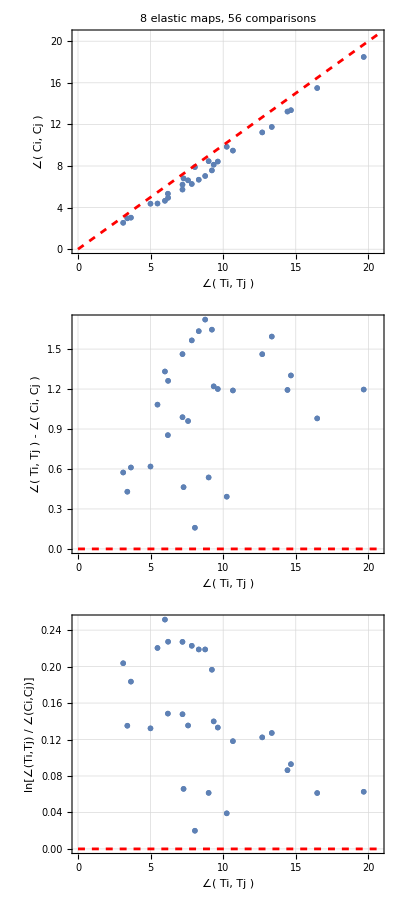

#### Brown and Abramson (2016) amphiboles

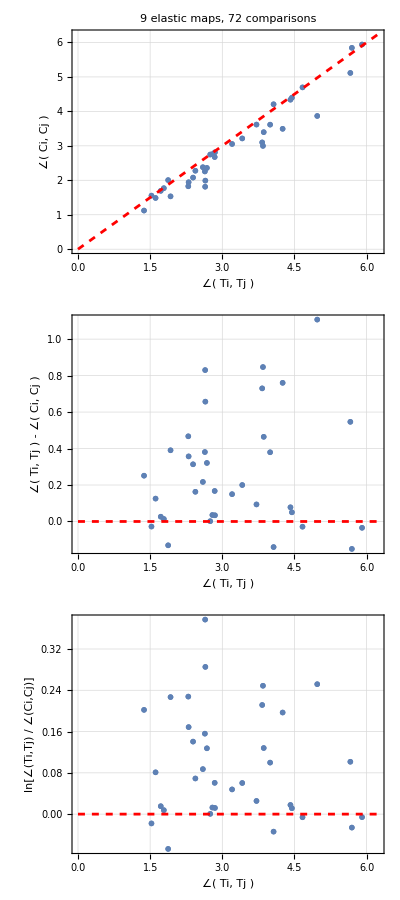

#### 28 maps in Zenodo collection (Tape and Gupta, 2024)

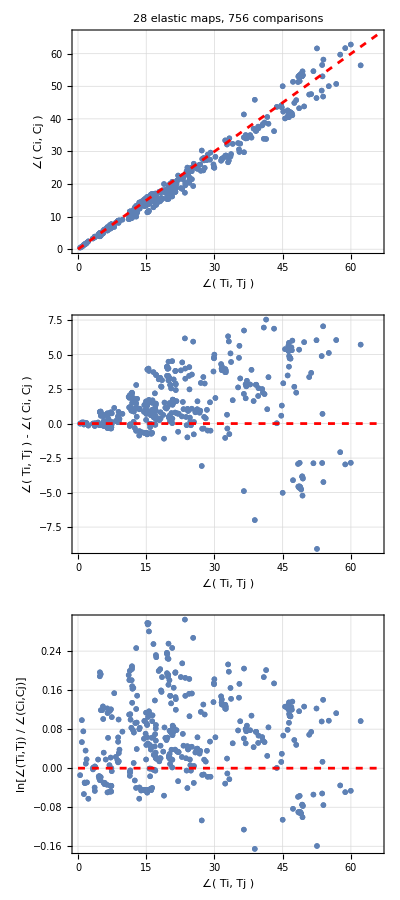

## Analytical expressions

```mathematica
Clear[a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v]
Clear[ax,bx,cx,dx,ex,fx,gx,hx,ix,jx,kx,lx,mx,nx,ox,px,qx,rx,sx,tx,ux,vx]
```

```mathematica
Tmat1=BlankSlate;
Cmat1=CmatOfTmat[Tmat1];
Tmat2=BlankSlatePrime;
Cmat2=CmatOfTmat[Tmat2];
```

```mathematica
PT=AngleMatrix[Tmat1,Tmat2];
PC=AngleMatrix[Cmat1,Cmat2];
```

#### Not very informative:

```mathematica
(*FullSimplify[PT]
FullSimplify[PC]*)
```

#### These took a LONG time and resulted in obvious expressions:

```mathematica
(* FullSimplify[PT/PC]
FullSimplify[PT-PC] *)
```